```mathematica
vals234=With[
{all=allGraphs5, count=5},
Monitor[Table[k->Map[Length,RedBlueGreen[k,all]],{k,Sort[Select[Keys[all],VertexCount[all[#,"graph"]]==count && ConnectedGraphQ[all[#,"graph"]]&]]}],k]
]
```

{760→{16,15,22},766→{16,15,22},768→{16,15,22},769→{20,10,23},814→{16,15,22},820→{16,15,22},822→{16,15,22},823→{20,10,23},840→{16,15,22},841→{20,10,23},846→{16,15,22},847→{20,10,23},849→{24,12,17},850→{26,7,20},976→{16,15,22},982→{16,15,22},984→{16,15,22},985→{20,10,23},1000→{16,15,22},1003→{20,10,23},1008→{16,15,22},1009→{24,12,17},1011→{20,10,23},1012→{26,7,20},1054→{16,15,22},1056→{16,15,22},1057→{24,12,17},1063→{20,10,23},1065→{20,10,23},1066→{26,7,20},1080→{16,15,22},1081→{20,10,23},1083→{20,10,23},1084→{26,7,20},1089→{20,10,23},1090→{26,7,20},1092→{26,7,20},1093→{30,4,19},2218→{16,15,22},2224→{16,15,22},2226→{16,15,22},2227→{20,10,23},2272→{16,15,22},2278→{16,15,22},2280→{16,15,22},2281→{20,10,23},2298→{16,15,22},2299→{20,10,23},2304→{16,15,22},2305→{20,10,23},2307→{24,12,17},2308→{26,7,20},2434→{16,15,22},2440→{16,15,22},2442→{16,15,22},2443→{20,10,23},2458→{16,15,22},2461→{20,10,23},2466→{16,15,22},2467→{24,12,17},2469→{20,10,23},2470→{26,7,20},2512→{16,15,22},2514→{16,15,22},2515→{24,12,17},2521→{20,10,23},2523→{20,10,23},2524→{26,7,20},2538→{16,15,22},2539→{20,10,23},2541→{20,10,23},2542→{26,7,20},2547→{20,10,23},2548→{26,7,20},2550→{26,7,20},2551→{30,4,19},2946→{16,15,22},2947→{20,10,23},2952→{16,15,22},2953→{20,10,23},2955→{24,12,17},2956→{26,7,20},3000→{16,15,22},3001→{20,10,23},3006→{16,15,22},3007→{20,10,23},3009→{24,12,17},3010→{26,7,20},3027→{24,12,17},3028→{26,7,20},3033→{24,12,17},3034→{26,7,20},3036→{34,10,9},3037→{35,5,13},3162→{16,15,22},3163→{20,10,23},3168→{16,15,22},3169→{20,10,23},3171→{24,12,17},3172→{26,7,20},3186→{16,15,22},3187→{20,10,23},3189→{20,10,23},3190→{25,7,21},3195→{27,11,15},3196→{31,8,14},3198→{31,8,14},3199→{34,5,14},3240→{16,15,22},3241→{20,10,23},3243→{27,11,15},3244→{31,8,14},3249→{20,10,23},3250→{25,7,21},3252→{31,8,14},3253→{34,5,14},3267→{24,12,17},3268→{26,7,20},3270→{31,8,14},3271→{34,5,14},3276→{31,8,14},3277→{34,5,14},3279→{38,6,9},3280→{40,3,10},6592→{16,15,22},6598→{16,15,22},6600→{16,15,22},6601→{20,10,23},6646→{16,15,22},6652→{16,15,22},6654→{16,15,22},6655→{20,10,23},6672→{16,15,22},6673→{20,10,23},6678→{16,15,22},6679→{20,10,23},6681→{24,12,17},6682→{26,7,20},6808→{16,15,22},6814→{16,15,22},6816→{16,15,22},6817→{20,10,23},6832→{16,15,22},6835→{20,10,23},6840→{16,15,22},6841→{24,12,17},6843→{20,10,23},6844→{26,7,20},6886→{16,15,22},6888→{16,15,22},6889→{24,12,17},6895→{20,10,23},6897→{20,10,23},6898→{26,7,20},6912→{16,15,22},6913→{20,10,23},6915→{20,10,23},6916→{26,7,20},6921→{20,10,23},6922→{26,7,20},6924→{26,7,20},6925→{30,4,19},7318→{16,15,22},7321→{20,10,23},7326→{16,15,22},7327→{24,12,17},7329→{20,10,23},7330→{26,7,20},7372→{16,15,22},7375→{20,10,23},7380→{16,15,22},7381→{24,12,17},7383→{20,10,23},7384→{26,7,20},7398→{16,15,22},7399→{20,10,23},7401→{20,10,23},7402→{25,7,21},7407→{27,11,15},7408→{31,8,14},7410→{31,8,14},7411→{34,5,14},7534→{16,15,22},7537→{20,10,23},7542→{16,15,22},7543→{24,12,17},7545→{20,10,23},7546→{26,7,20},7561→{24,12,17},7564→{26,7,20},7569→{24,12,17},7570→{34,10,9},7572→{26,7,20},7573→{35,5,13},7614→{16,15,22},7615→{27,11,15},7617→{20,10,23},7618→{31,8,14},7623→{20,10,23},7624→{31,8,14},7626→{25,7,21},7627→{34,5,14},7641→{24,12,17},7642→{31,8,14},7644→{26,7,20},7645→{34,5,14},7650→{31,8,14},7651→{38,6,9},7653→{34,5,14},7654→{40,3,10},8776→{16,15,22},8778→{16,15,22},8779→{24,12,17},8785→{20,10,23},8787→{20,10,23},8788→{26,7,20},8830→{16,15,22},8832→{16,15,22},8833→{24,12,17},8839→{20,10,23},8841→{20,10,23},8842→{26,7,20},8856→{16,15,22},8857→{20,10,23},8859→{27,11,15},8860→{31,8,14},8865→{20,10,23},8866→{25,7,21},8868→{31,8,14},8869→{34,5,14},8992→{16,15,22},8994→{16,15,22},8995→{24,12,17},9001→{20,10,23},9003→{20,10,23},9004→{26,7,20},9018→{16,15,22},9019→{27,11,15},9021→{20,10,23},9022→{31,8,14},9027→{20,10,23},9028→{31,8,14},9030→{25,7,21},9031→{34,5,14},9073→{24,12,17},9075→{24,12,17},9076→{34,10,9},9082→{26,7,20},9084→{26,7,20},9085→{35,5,13},9099→{24,12,17},9100→{31,8,14},9102→{31,8,14},9103→{38,6,9},9108→{26,7,20},9109→{34,5,14},9111→{34,5,14},9112→{40,3,10},9504→{16,15,22},9505→{20,10,23},9507→{20,10,23},9508→{26,7,20},9513→{20,10,23},9514→{26,7,20},9516→{26,7,20},9517→{30,4,19},9558→{16,15,22},9559→{20,10,23},9561→{20,10,23},9562→{26,7,20},9567→{20,10,23},9568→{26,7,20},9570→{26,7,20},9571→{30,4,19},9585→{24,12,17},9586→{26,7,20},9588→{31,8,14},9589→{34,5,14},9594→{31,8,14},9595→{34,5,14},9597→{38,6,9},9598→{40,3,10},9720→{16,15,22},9721→{20,10,23},9723→{20,10,23},9724→{26,7,20},9729→{20,10,23},9730→{26,7,20},9732→{26,7,20},9733→{30,4,19},9747→{24,12,17},9748→{31,8,14},9750→{26,7,20},9751→{34,5,14},9756→{31,8,14},9757→{38,6,9},9759→{34,5,14},9760→{40,3,10},9801→{24,12,17},9802→{31,8,14},9804→{31,8,14},9805→{38,6,9},9810→{26,7,20},9811→{34,5,14},9813→{34,5,14},9814→{40,3,10},9828→{34,10,9},9829→{38,6,9},9831→{38,6,9},9832→{43,4,6},9837→{38,6,9},9838→{43,4,6},9840→{43,4,6},9841→{47,2,4},19714→{16,15,22},19720→{16,15,22},19722→{16,15,22},19723→{20,10,23},19768→{16,15,22},19774→{16,15,22},19776→{16,15,22},19777→{20,10,23},19794→{16,15,22},19795→{20,10,23},19800→{16,15,22},19801→{20,10,23},19803→{24,12,17},19804→{26,7,20},19930→{16,15,22},19936→{16,15,22},19938→{16,15,22},19939→{20,10,23},19954→{16,15,22},19957→{20,10,23},19962→{16,15,22},19963→{24,12,17},19965→{20,10,23},19966→{26,7,20},20008→{16,15,22},20010→{16,15,22},20011→{24,12,17},20017→{20,10,23},20019→{20,10,23},20020→{26,7,20},20034→{16,15,22},20035→{20,10,23},20037→{20,10,23},20038→{26,7,20},20043→{20,10,23},20044→{26,7,20},20046→{26,7,20},20047→{30,4,19},20416→{16,15,22},20422→{16,15,22},20424→{16,15,22},20425→{20,10,23},20443→{20,10,23},20449→{20,10,23},20451→{20,10,23},20452→{25,7,21},20496→{16,15,22},20497→{24,12,17},20502→{16,15,22},20503→{24,12,17},20505→{27,11,15},20506→{31,8,14},20523→{20,10,23},20524→{26,7,20},20529→{20,10,23},20530→{26,7,20},20532→{31,8,14},20533→{34,5,14},20656→{16,15,22},20659→{24,12,17},20664→{16,15,22},20665→{27,11,15},20667→{24,12,17},20668→{31,8,14},20683→{20,10,23},20686→{26,7,20},20691→{20,10,23},20692→{31,8,14},20694→{26,7,20},20695→{34,5,14},20736→{16,15,22},20737→{24,12,17},20739→{24,12,17},20740→{34,10,9},20745→{20,10,23},20746→{31,8,14},20748→{31,8,14},20749→{38,6,9},20763→{20,10,23},20764→{26,7,20},20766→{26,7,20},20767→{35,5,13},20772→{25,7,21},20773→{34,5,14},20775→{34,5,14},20776→{40,3,10},21874→{16,15,22},21880→{16,15,22},21882→{16,15,22},21883→{20,10,23},21900→{16,15,22},21901→{24,12,17},21906→{16,15,22},21907→{24,12,17},21909→{27,11,15},21910→{31,8,14},21955→{20,10,23},21961→{20,10,23},21963→{20,10,23},21964→{25,7,21},21981→{20,10,23},21982→{26,7,20},21987→{20,10,23},21988→{26,7,20},21990→{31,8,14},21991→{34,5,14},22114→{16,15,22},22116→{16,15,22},22117→{27,11,15},22123→{24,12,17},22125→{24,12,17},22126→{31,8,14},22140→{16,15,22},22141→{24,12,17},22143→{20,10,23},22144→{31,8,14},22149→{24,12,17},22150→{34,10,9},22152→{31,8,14},22153→{38,6,9},22195→{20,10,23},22197→{20,10,23},22198→{31,8,14},22204→{26,7,20},22206→{26,7,20},22207→{34,5,14},22221→{20,10,23},22222→{26,7,20},22224→{25,7,21},22225→{34,5,14},22230→{26,7,20},22231→{35,5,13},22233→{34,5,14},22234→{40,3,10},22602→{16,15,22},22603→{20,10,23},22608→{16,15,22},22609→{20,10,23},22611→{24,12,17},22612→{26,7,20},22629→{20,10,23},22630→{26,7,20},22635→{20,10,23},22636→{26,7,20},22638→{31,8,14},22639→{34,5,14},22683→{20,10,23},22684→{26,7,20},22689→{20,10,23},22690→{26,7,20},22692→{31,8,14},22693→{34,5,14},22710→{26,7,20},22711→{30,4,19},22716→{26,7,20},22717→{30,4,19},22719→{38,6,9},22720→{40,3,10},22842→{16,15,22},22843→{20,10,23},22845→{24,12,17},22846→{31,8,14},22851→{24,12,17},22852→{31,8,14},22854→{34,10,9},22855→{38,6,9},22869→{20,10,23},22870→{26,7,20},22872→{26,7,20},22873→{34,5,14},22878→{31,8,14},22879→{38,6,9},22881→{38,6,9},22882→{43,4,6},22923→{20,10,23},22924→{26,7,20},22926→{31,8,14},22927→{38,6,9},22932→{26,7,20},22933→{34,5,14},22935→{38,6,9},22936→{43,4,6},22950→{26,7,20},22951→{30,4,19},22953→{34,5,14},22954→{40,3,10},22959→{34,5,14},22960→{40,3,10},22962→{43,4,6},22963→{47,2,4},26248→{16,15,22},26254→{16,15,22},26256→{16,15,22},26257→{20,10,23},26272→{16,15,22},26275→{24,12,17},26280→{16,15,22},26281→{27,11,15},26283→{24,12,17},26284→{31,8,14},26326→{16,15,22},26328→{16,15,22},26329→{27,11,15},26335→{24,12,17},26337→{24,12,17},26338→{31,8,14},26352→{16,15,22},26353→{20,10,23},26355→{24,12,17},26356→{31,8,14},26361→{24,12,17},26362→{31,8,14},26364→{34,10,9},26365→{38,6,9},26491→{20,10,23},26497→{20,10,23},26499→{20,10,23},26500→{25,7,21},26515→{20,10,23},26518→{26,7,20},26523→{20,10,23},26524→{31,8,14},26526→{26,7,20},26527→{34,5,14},26569→{20,10,23},26571→{20,10,23},26572→{31,8,14},26578→{26,7,20},26580→{26,7,20},26581→{34,5,14},26595→{20,10,23},26596→{25,7,21},26598→{26,7,20},26599→{34,5,14},26604→{26,7,20},26605→{34,5,14},26607→{35,5,13},26608→{40,3,10},26974→{16,15,22},26977→{20,10,23},26982→{16,15,22},26983→{24,12,17},26985→{20,10,23},26986→{26,7,20},27001→{20,10,23},27004→{26,7,20},27009→{20,10,23},27010→{31,8,14},27012→{26,7,20},27013→{34,5,14},27054→{16,15,22},27055→{24,12,17},27057→{20,10,23},27058→{31,8,14},27063→{24,12,17},27064→{34,10,9},27066→{31,8,14},27067→{38,6,9},27081→{20,10,23},27082→{26,7,20},27084→{26,7,20},27085→{34,5,14},27090→{31,8,14},27091→{38,6,9},27093→{38,6,9},27094→{43,4,6},27217→{20,10,23},27220→{26,7,20},27225→{20,10,23},27226→{31,8,14},27228→{26,7,20},27229→{34,5,14},27244→{26,7,20},27247→{30,4,19},27252→{26,7,20},27253→{38,6,9},27255→{30,4,19},27256→{40,3,10},27297→{20,10,23},27298→{31,8,14},27300→{26,7,20},27301→{38,6,9},27306→{26,7,20},27307→{38,6,9},27309→{34,5,14},27310→{43,4,6},27324→{26,7,20},27325→{34,5,14},27327→{30,4,19},27328→{40,3,10},27333→{34,5,14},27334→{43,4,6},27336→{40,3,10},27337→{47,2,4},28432→{16,15,22},28434→{16,15,22},28435→{24,12,17},28441→{20,10,23},28443→{20,10,23},28444→{26,7,20},28458→{16,15,22},28459→{24,12,17},28461→{24,12,17},28462→{34,10,9},28467→{20,10,23},28468→{31,8,14},28470→{31,8,14},28471→{38,6,9},28513→{20,10,23},28515→{20,10,23},28516→{31,8,14},28522→{26,7,20},28524→{26,7,20},28525→{34,5,14},28539→{20,10,23},28540→{26,7,20},28542→{31,8,14},28543→{38,6,9},28548→{26,7,20},28549→{34,5,14},28551→{38,6,9},28552→{43,4,6},28675→{20,10,23},28677→{20,10,23},28678→{31,8,14},28684→{26,7,20},28686→{26,7,20},28687→{34,5,14},28701→{20,10,23},28702→{31,8,14},28704→{26,7,20},28705→{38,6,9},28710→{26,7,20},28711→{38,6,9},28713→{34,5,14},28714→{43,4,6},28756→{26,7,20},28758→{26,7,20},28759→{38,6,9},28765→{30,4,19},28767→{30,4,19},28768→{40,3,10},28782→{26,7,20},28783→{34,5,14},28785→{34,5,14},28786→{43,4,6},28791→{30,4,19},28792→{40,3,10},28794→{40,3,10},28795→{47,2,4},29160→{16,15,22},29161→{20,10,23},29163→{20,10,23},29164→{26,7,20},29169→{20,10,23},29170→{26,7,20},29172→{26,7,20},29173→{30,4,19},29187→{20,10,23},29188→{26,7,20},29190→{26,7,20},29191→{35,5,13},29196→{25,7,21},29197→{34,5,14},29199→{34,5,14},29200→{40,3,10},29241→{20,10,23},29242→{26,7,20},29244→{25,7,21},29245→{34,5,14},29250→{26,7,20},29251→{35,5,13},29253→{34,5,14},29254→{40,3,10},29268→{26,7,20},29269→{30,4,19},29271→{34,5,14},29272→{40,3,10},29277→{34,5,14},29278→{40,3,10},29280→{43,4,6},29281→{47,2,4},29403→{20,10,23},29404→{25,7,21},29406→{26,7,20},29407→{34,5,14},29412→{26,7,20},29413→{34,5,14},29415→{35,5,13},29416→{40,3,10},29430→{26,7,20},29431→{34,5,14},29433→{30,4,19},29434→{40,3,10},29439→{34,5,14},29440→{43,4,6},29442→{40,3,10},29443→{47,2,4},29484→{26,7,20},29485→{34,5,14},29487→{34,5,14},29488→{43,4,6},29493→{30,4,19},29494→{40,3,10},29496→{40,3,10},29497→{47,2,4},29511→{35,5,13},29512→{40,3,10},29514→{40,3,10},29515→{47,2,4},29520→{40,3,10},29521→{47,2,4},29523→{47,2,4},29524→{52,1,0}}

```mathematica
Max[Map[#[[2,3]]&,vals234]]
```

23

```mathematica
Partition
```

```mathematica
Sort[Table[allGraphs5[k,"graph"],{k,Map[#[[1]]&,Select[vals234,#[[2,3]]==23&]]}],IsomorphicGraphQ[#1,#2]&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ToAssoc[all_]:=Block[{result={},g, h,found,i},
Table[
found=False;
g=all[k,"graph"];
For[i=1,i≤Length[result],i++,
h=all[First[result[[i]]],"graph"];
If[IsomorphicGraphQ[g,h],
AppendTo[result[[i]],k];
found=True;
i=Length[all]+1
]
];
If[!found,AppendTo[result,{k}]]
,{k,Keys[all]}
];
result
]
```

```mathematica
Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&RedBlueGreen[#,allGraphs5][[3]]==RedBlueGreen[FindComplement[#,allGraphs5],allGraphs5][[3]]&]
```

{0,29524}

```mathematica
Map[Length,ToAssoc[allGraphs4]]//Sort
```

{1,1,1,3,3,4,4,6,6,6,6,7,7,12,12,12,18,18}

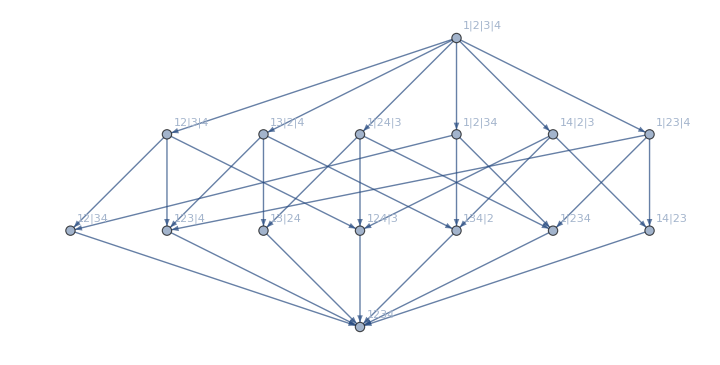
{-Graphics-365-Graphics-2 n1234-n12x34-n134x2-n1x234+n1x2x34x^3-3 x^2+2 x
(x-2) (x-1) x
 *  * 0062460
-Graphics-}

```mathematica
Table[SummaryPrintGood[k],{k,{365}}]
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
vals234=With[
{all=allGraphs5, count=5},
Monitor[Table[Map[Length,RedBlueGreen[k,all]],{k,Sort[Keys[all]]}],k]
];
```

```mathematica
ListPointPlot3D[vals234,PlotRange->All,Filling->Bottom]
```

-Graphics3D-

```mathematica
With[
{all=allGraphs6, count=6},
Length[Select[Keys[all],VertexCount[all[#,"graph"]]==count && ConnectedGraphQ[all[#,"graph"]]&]]
]
```

26704

```mathematica
With[
{all=allGraphs6, count=6},
Monitor[Table[Map[Length,Most [RedBlueGreen[k,all]]],{k,Sort[Select[Keys[all],VertexCount[all[#,"graph"]]==count&]]}],k]
]
```

$Aborted

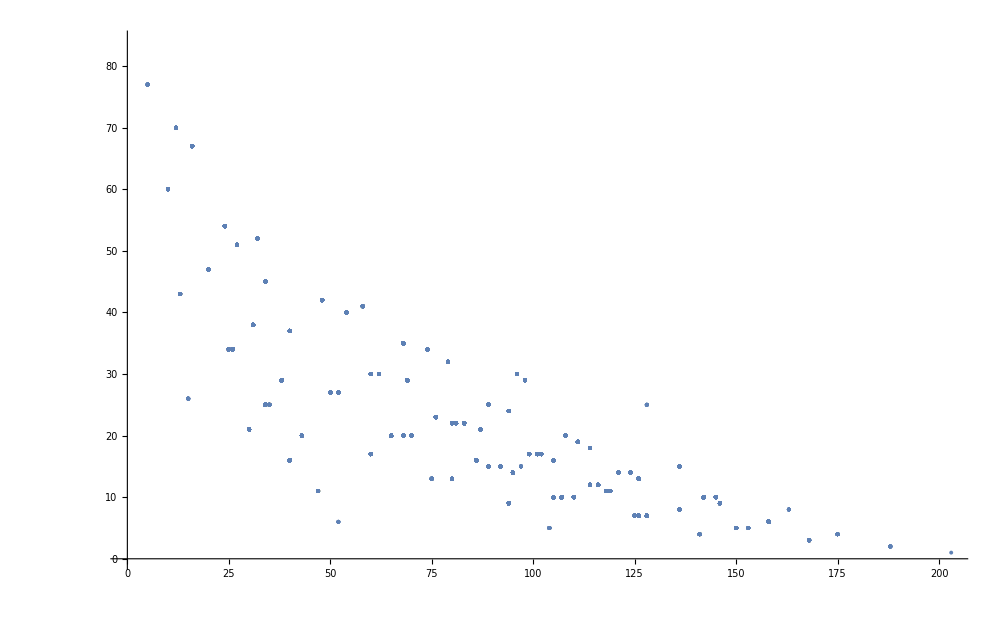

```mathematica
ListPlot[%]
```